```mathematica
raw=Import["C:/Users/gram/Documents/GitHub/smoothie/20160510_list.txt","Data"];
```

```mathematica
raw//Length
```

70

```mathematica
raw[[1]]
```

{Almond Mocha High Protein,345,9,1,80,51,42,37,30,195,2}

```mathematica
labels=raw[[All,1]];
```

```mathematica
sugar=Table[raw[[i,8]],{i,1,Length[raw]}];
```

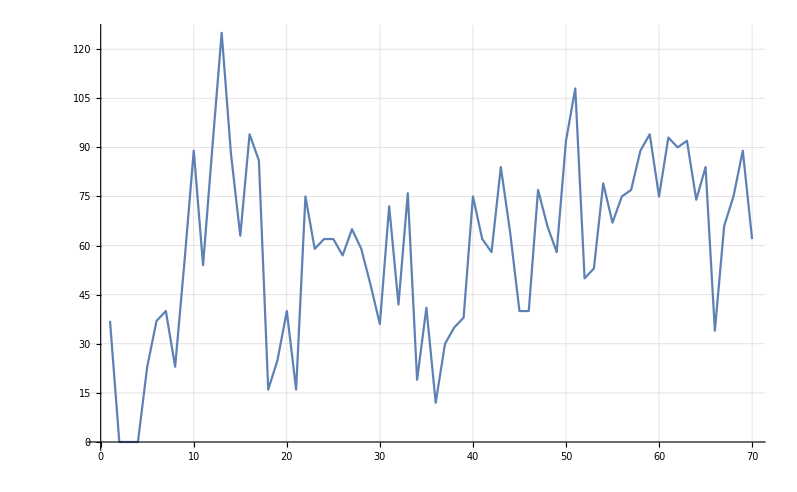

```mathematica
ListPlot[sugar,Joined->True,GridLines->Automatic]
```

So the lowest sugar smoothies are 2,3,4,18,21,34,36

```mathematica
labels[[{2,3,4,18,21,34,36}]]
```

{Gladiator® Chocolate,Gladiator® Strawberry,Gladiator® Vanilla,Lean1™ Chocolate,Lean1™ Vanilla,The Shredder - Chocolate™,The Shredder - Vanilla™}

```mathematica
proSugIndex=raw[[All,9]]/raw[[All,8]]//N
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{0.810811,ComplexInfinity,ComplexInfinity,ComplexInfinity,1.17391,0.810811,0.65,1.17391,0.345455,0.213483,0.333333,0.266667,0.2,0.261364,0.380952,0.159574,0.127907,1.1875,0.64,0.425,1.1875,0.0533333,0.186441,0.177419,0.193548,0.210526,0.0461538,0.,0.3125,0.194444,0.111111,0.166667,0.0131579,1.52632,0.731707,3.,0.6,0.314286,0.263158,0.0666667,0.016129,0.0172414,0.,0.109375,0.1,0.2,0.0649351,0.0454545,0.0344828,0.0108696,0.00925926,0.,0.0566038,0.0126582,0.134328,0.0533333,0.155844,0.011236,0.0106383,0.0666667,0.0107527,0.0444444,0.076087,0.0135135,0.047619,0.382353,0.136364,0.12,0.011236,0.016129}

```mathematica
proSugIndex[[{2,3,4}]]=1.8
```

1.8

```mathematica
proSugIndex
```

{0.810811,1.3,1.3,1.3,1.17391,0.810811,0.65,1.17391,0.345455,0.213483,0.333333,0.266667,0.2,0.261364,0.380952,0.159574,0.127907,1.1875,0.64,0.425,1.1875,0.0533333,0.186441,0.177419,0.193548,0.210526,0.0461538,0.,0.3125,0.194444,0.111111,0.166667,0.0131579,1.52632,0.731707,3.,0.6,0.314286,0.263158,0.0666667,0.016129,0.0172414,0.,0.109375,0.1,0.2,0.0649351,0.0454545,0.0344828,0.0108696,0.00925926,0.,0.0566038,0.0126582,0.134328,0.0533333,0.155844,0.011236,0.0106383,0.0666667,0.0107527,0.0444444,0.076087,0.0135135,0.047619,0.382353,0.136364,0.12,0.011236,0.016129}

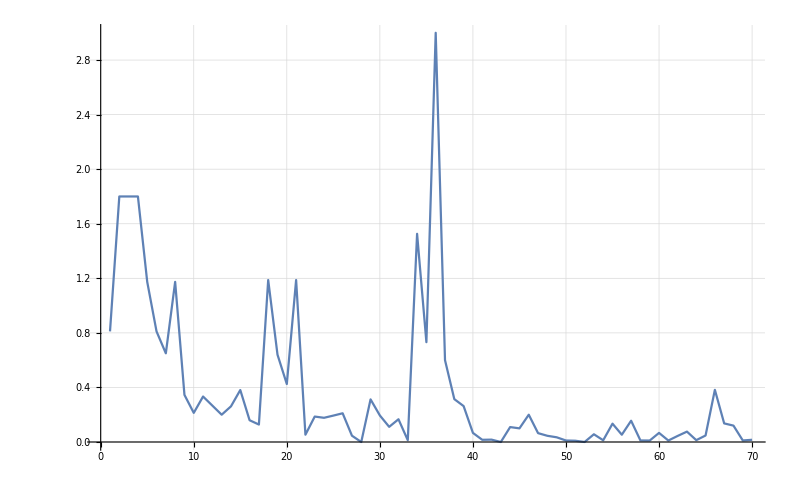

```mathematica
ListPlot[proSugIndex,Joined->True,GridLines->Automatic,PlotRange->All]
```

```mathematica
Position[proSugIndex,3.0]
```

{{36}}

```mathematica
labels[[36]]
```

The Shredder - Vanilla™